#### Exporting data: an example

```mathematica
(*SetDirectory[NotebookDirectory[]];*)
(*Export["gpsDayEpoch.pdf",gpsDayEpoch,"PDF",ImageSize->Full,"AllowRasterization"->False]*)

(*
	Uncomment the above two lines and place these lines after you have graffed something 
	For example, say you named a graph "gpsDayEpoch"; be sure to rewrite the second line 
	depending on your needs. Files will be exported in the PDF format to wherever the 
	MMA notebook is located.
*)
```

#### Importing data and saving columns

```mathematica
peListFlatPriors=Import["/Users/jitensingh/Sync Folder/Research/Successive Sign Flips/PE_list_Dec2021 - Filtered Flat Prior 5k Template Search.csv","Dataset","HeaderLines"->1]

gpsDays=Table[peListFlatPriors[[i,1]],{i,Length[peListFlatPriors]}];
utcDates=Table[peListFlatPriors[[i,2]],{i,Length[peListFlatPriors]}];
epochs=Table[peListFlatPriors[[i,3]],{i,Length[peListFlatPriors]}];
numClocks=Table[peListFlatPriors[[i,4]],{i,Length[peListFlatPriors]}];
SNRs=Table[peListFlatPriors[[i,5]],{i,Length[peListFlatPriors]}];
absSNR=Abs[SNRs];
chi2=Table[peListFlatPriors[[i,7]],{i,Length[peListFlatPriors]}];
chi2Thresh=Table[peListFlatPriors[[i,8]],{i,Length[peListFlatPriors]}];
hhat=Table[peListFlatPriors[[i,9]],{i,Length[peListFlatPriors]}];
vPerp=Table[peListFlatPriors[[i,10]],{i,Length[peListFlatPriors]}];
cosTheta=Table[peListFlatPriors[[i,12]],{i,Length[peListFlatPriors]}];
```

Dataset[<>]

#### GPS Day vs. Epoch (30s)

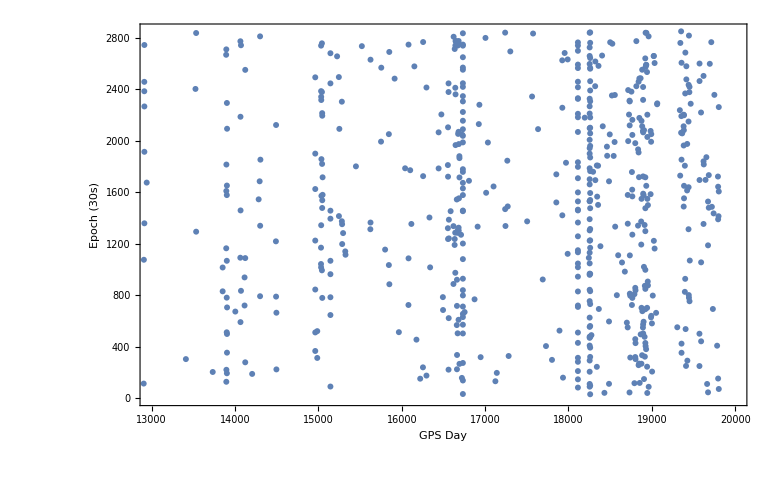

```mathematica
gpsDayEpoch=ListPlot[Transpose[{gpsDays,epochs}],PlotRange->{{13000,20000},All},Frame->True,FrameTicks->Automatic,FrameTicksStyle->Directive[FontFamily->"cmr10",FontSize->20,FontColor->Black],FrameLabel->{Style["GPS Day",FontFamily->"cmr10",SingleLetterItalics->False,FontSize->25,FontColor->Black],Style["Epoch (30s)",FontFamily->"cmr10",FontSize->25,FontColor->Black]}]
```

#### GPS Day vs. SNRs

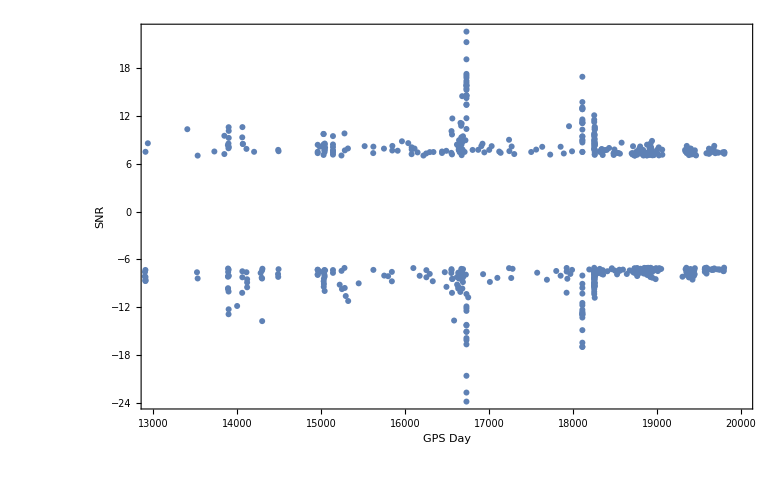

```mathematica
gpsDaySNRs=ListPlot[Transpose[{gpsDays,SNRs}],PlotRange->{{13000,20000},All},Frame->True,FrameTicks->{Automatic,{-20,-10,0,10,20},None},FrameTicksStyle->Directive[FontFamily->"cmr10",FontSize->20,FontColor->Black],FrameLabel->{Style["GPS Day",FontFamily->"cmr10",SingleLetterItalics->False,FontSize->25,FontColor->Black],Style["SNR",FontFamily->"cmr10",FontSize->25,FontColor->Black]} ]
```

#### GPS Day vs. |SNRs|

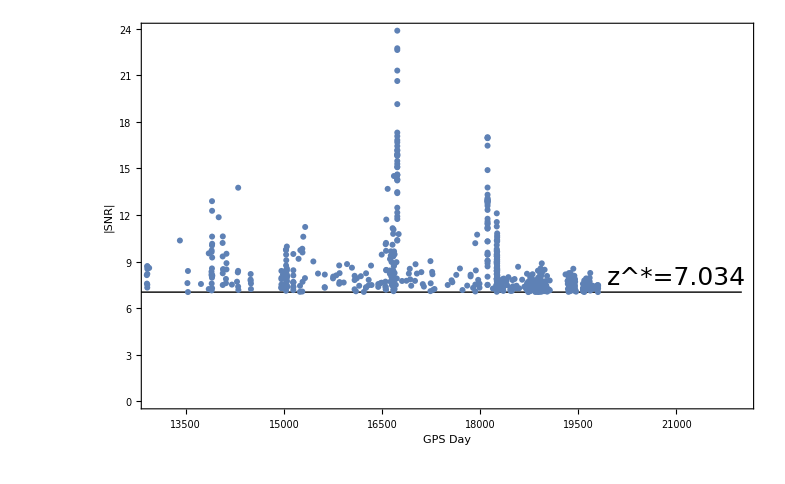

```mathematica
thresh=7.034;
gpsDayAbsSNRs=ListPlot[Transpose[{gpsDays,absSNR}],PlotRange->{{13000,22000},All},Frame->True,FrameTicks->{Automatic,{-20,-10,0,10,20},None},FrameTicksStyle->Directive[FontFamily->"cmr10",FontSize->20,FontColor->Black],FrameLabel->{Style["GPS Day",FontFamily->"cmr10",SingleLetterItalics->False,FontSize->25,FontColor->Black],Style["|SNR|",FontFamily->"cmr10",FontSize->25,FontColor->Black]} ,Epilog->{Line[{{0,thresh},{22000,thresh}}],Text[Style["z^*=7.034",FontFamily->"cmr10",SingleLetterItalics->False,FontSize->25,FontColor->Black],{21000,thresh+1}]}]
```

```mathematica
Max[absSNR]
```

23.8612

#### GPS Day vs. χ^2/d.o.f.

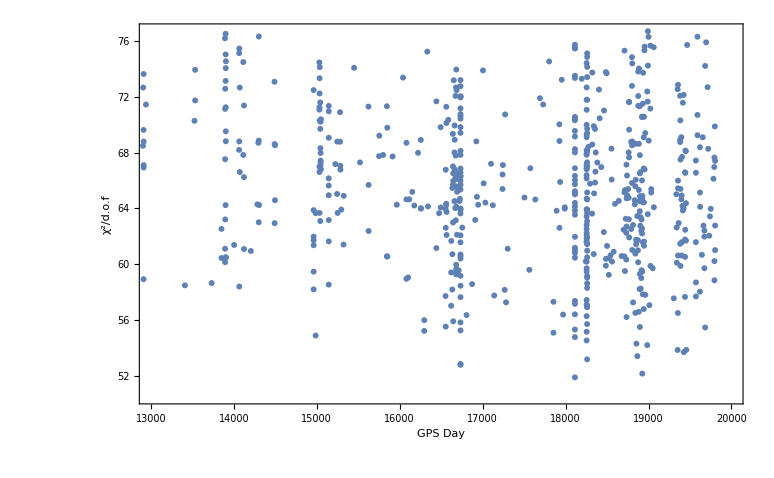

```mathematica
chiDOF=chi2/numClocks;
gpsDayChiDof=ListPlot[Transpose[{gpsDays,chiDOF}],PlotRange->{{13000,20000},All},Frame->True,FrameTicks->{Automatic,{-20,-10,0,10,20},None},FrameTicksStyle->Directive[FontFamily->"cmr10",FontSize->20,FontColor->Black],FrameLabel->{Style["GPS Day",FontFamily->"cmr10",SingleLetterItalics->False,FontSize->25,FontColor->Black],Style["χ^2/d.o.f",SingleLetterItalics->False,FontFamily->"cmr10",FontSize->25,FontColor->Black]} ]
```

#### SNRs vs. χ^2/d.o.f.

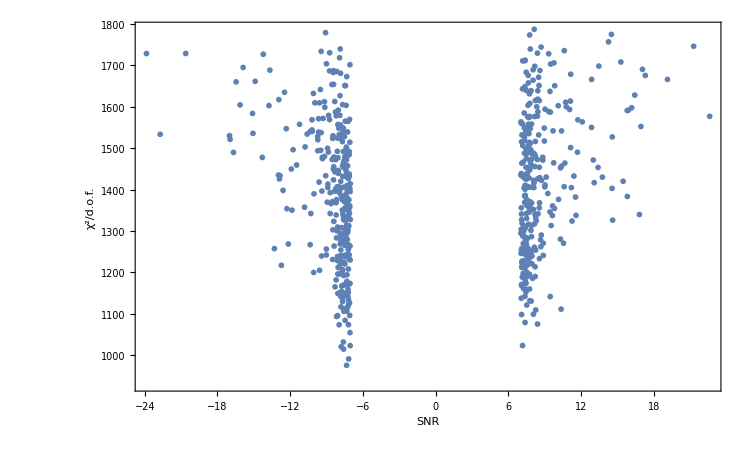

```mathematica
snrChiDof=ListPlot[Transpose[{SNRs,chi2}],PlotRange->{All,All},Frame->True,FrameTicks->{{-20,-15,-10,-5,0,5,10,15,20},Automatic,None},FrameTicksStyle->Directive[FontFamily->"cmr10",FontSize->20,FontColor->Black],FrameLabel->{Style["SNR",FontFamily->"cmr10",SingleLetterItalics->False,FontSize->25,FontColor->Black],Style["χ^2/d.o.f.",SingleLetterItalics->False,FontFamily->"cmr10",FontSize->25,FontColor->Black]} ]
```

#### |SNRs| vs. χ^2/d.o.f.

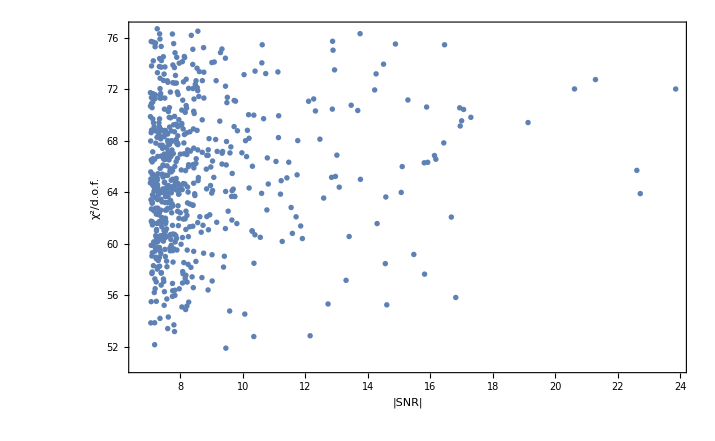

```mathematica
absSNRsChiDof=ListPlot[Transpose[{absSNR,chiDOF}],PlotRange->{All,All},Frame->True,FrameTicks->Automatic,FrameTicksStyle->Directive[FontFamily->"cmr10",FontSize->20,FontColor->Black],FrameLabel->{Style["|SNR|",FontFamily->"cmr10",SingleLetterItalics->False,FontSize->25,FontColor->Black],Style["χ^2/d.o.f.",SingleLetterItalics->False,FontFamily->"cmr10",FontSize->25,FontColor->Black]}]
```

#### SNRs vs. Number of Clocks

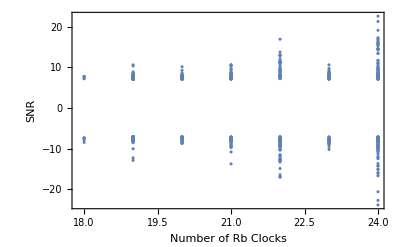

```mathematica
SNRsNumClocks=ListPlot[Transpose[{numClocks,SNRs}],PlotRange->{All,All},Frame->True,FrameTicks->Automatic,FrameTicksStyle->Directive[FontFamily->"cmr10",FontSize->20,FontColor->Black],FrameLabel->{Style["Number of Rb Clocks",FontFamily->"cmr10",SingleLetterItalics->False,FontSize->25,FontColor->Black],Style["SNR",FontFamily->"cmr10",FontSize->25,FontColor->Black]}]
```

#### |SNRs| vs. Number of Clocks

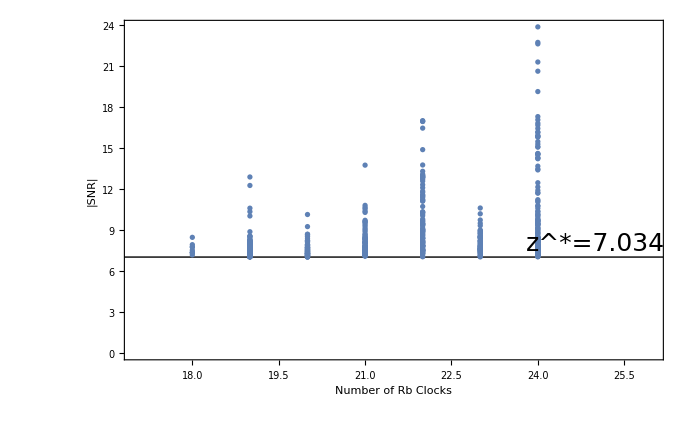

```mathematica
absSNRsNumClocks=ListPlot[Transpose[{numClocks,absSNR}],PlotRange->{{17,26},All},Frame->True,FrameTicks->Automatic,FrameTicksStyle->Directive[FontFamily->"cmr10",FontSize->20,FontColor->Black],FrameLabel->{Style["Number of Rb Clocks",FontFamily->"cmr10",SingleLetterItalics->False,FontSize->25,FontColor->Black],Style["|SNR|",FontFamily->"cmr10",FontSize->25,FontColor->Black]},Epilog->{Line[{{0,thresh},{22000,thresh}}],Text[Style["z^*=7.034",FontFamily->"cmr10",SingleLetterItalics->False,FontSize->25,FontColor->Black],{25,thresh+1}]}]
```

#### Number of clocks vs. χ^2/d.o.f.

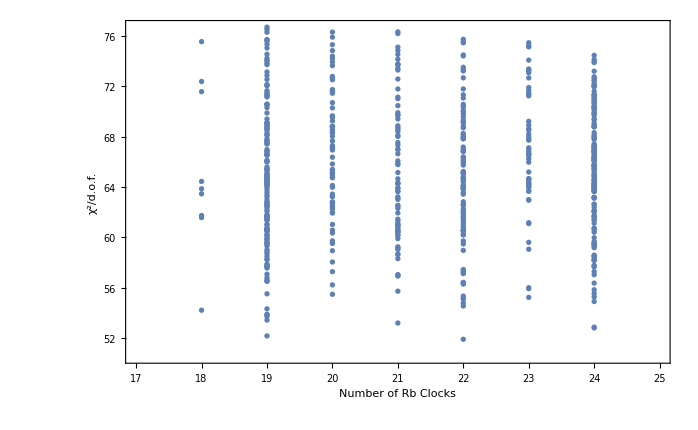

```mathematica
numClocksChiDof=ListPlot[Transpose[{numClocks,chiDOF}],PlotRange->{{17,25},All},Frame->True,FrameTicks->Automatic,FrameTicksStyle->Directive[FontFamily->"cmr10",FontSize->20,FontColor->Black],FrameLabel->{Style["Number of Rb Clocks",FontFamily->"cmr10",SingleLetterItalics->False,FontSize->25,FontColor->Black],Style["χ^2/d.o.f.",FontFamily->"cmr10",FontSize->25,FontColor->Black]}]
```

#### SNRs vs. v_⊥ (km/s)

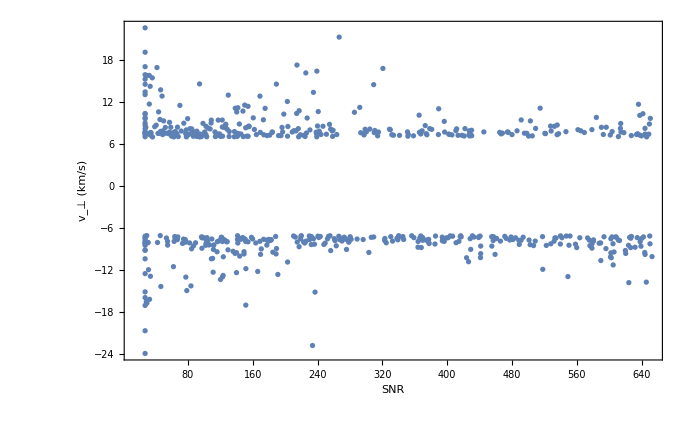

```mathematica
SNRsVPerp=ListPlot[Transpose[{vPerp,SNRs}],PlotRange->{All,All},Frame->True,FrameTicks->Automatic,FrameTicksStyle->Directive[FontFamily->"cmr10",FontSize->20,FontColor->Black],FrameLabel->{Style["SNR",FontFamily->"cmr10",SingleLetterItalics->False,FontSize->25,FontColor->Black],Style["v_⊥ (km/s)",SingleLetterItalics->False,FontFamily->"cmr10",FontSize->25,FontColor->Black]}]
```

#### |SNRs| vs. v_⊥

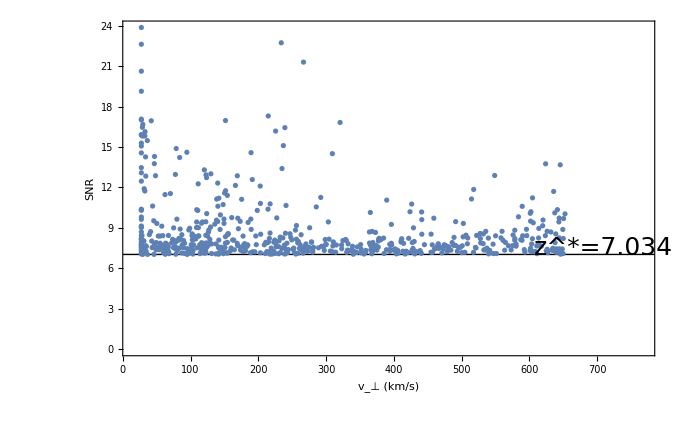

```mathematica
absSNRsVPerp=ListPlot[Transpose[{vPerp,absSNR}],PlotRange->{{15,770},All},Frame->True,FrameTicks->Automatic,FrameTicksStyle->Directive[FontFamily->"cmr10",FontSize->20,FontColor->Black],FrameLabel->{Style["v_⊥ (km/s)",FontFamily->"cmr10",SingleLetterItalics->False,FontSize->25,FontColor->Black],Style["SNR",FontFamily->"cmr10",FontSize->25,FontColor->Black]},Epilog->{Line[{{0,thresh},{22000,thresh}}],Text[Style["z^*=7.034",FontFamily->"cmr10",SingleLetterItalics->False,FontSize->25,FontColor->Black],{710,thresh+0.5}]}]
```

#### SNRs vs. ĥ (ns)

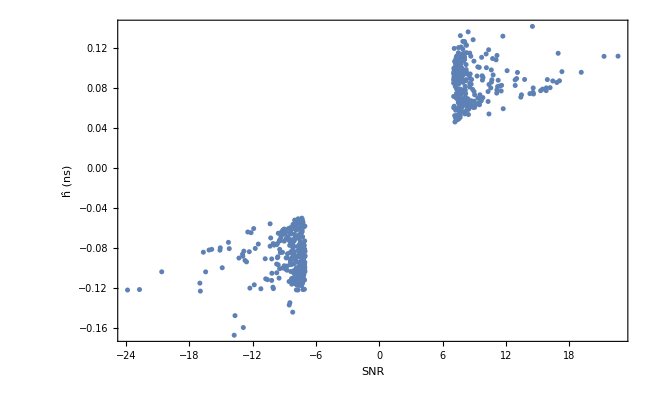

```mathematica
SNRsHHat=ListPlot[Transpose[{SNRs,hhat}],PlotRange->{All,All},Frame->True,FrameTicks->Automatic,FrameTicksStyle->Directive[FontFamily->"cmr10",FontSize->20,FontColor->Black],FrameLabel->{Style["SNR",FontFamily->"cmr10",SingleLetterItalics->False,FontSize->25,FontColor->Black],Style["ĥ (ns)",SingleLetterItalics->False,FontFamily->"cmr10",FontSize->25,FontColor->Black]}]
```

#### |SNRs| vs. ĥ (ns)

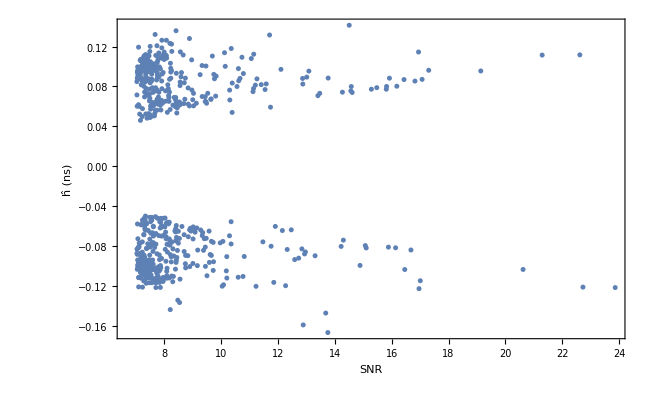

```mathematica
absSNRsHHat=ListPlot[Transpose[{absSNR,hhat}],PlotRange->{All,All},Frame->True,FrameTicks->Automatic,FrameTicksStyle->Directive[FontFamily->"cmr10",FontSize->20,FontColor->Black],FrameLabel->{Style["SNR",FontFamily->"cmr10",SingleLetterItalics->False,FontSize->25,FontColor->Black],Style["ĥ (ns)",SingleLetterItalics->False,FontFamily->"cmr10",FontSize->25,FontColor->Black]}]
```

#### χ^2/d.o.f. vs. ĥ (ns)

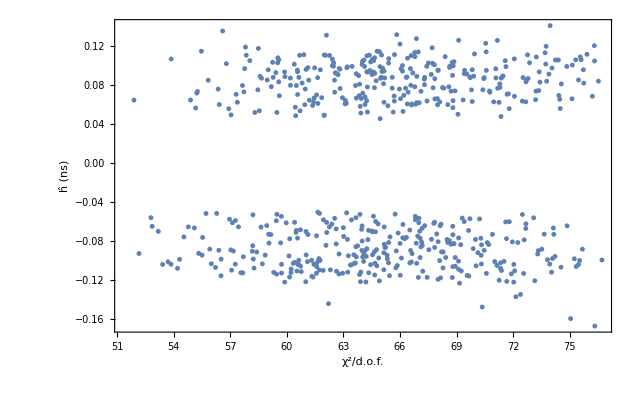

```mathematica
chiDofHHat=ListPlot[Transpose[{chiDOF,hhat}],PlotRange->{All,All},Frame->True,FrameTicks->Automatic,FrameTicksStyle->Directive[FontFamily->"cmr10",FontSize->20,FontColor->Black],FrameLabel->{Style["χ^2/d.o.f.",FontFamily->"cmr10",SingleLetterItalics->False,FontSize->25,FontColor->Black],Style["ĥ (ns)",SingleLetterItalics->False,FontFamily->"cmr10",FontSize->25,FontColor->Black]}]
```

#### GPS Day vs. ĥ (ns)

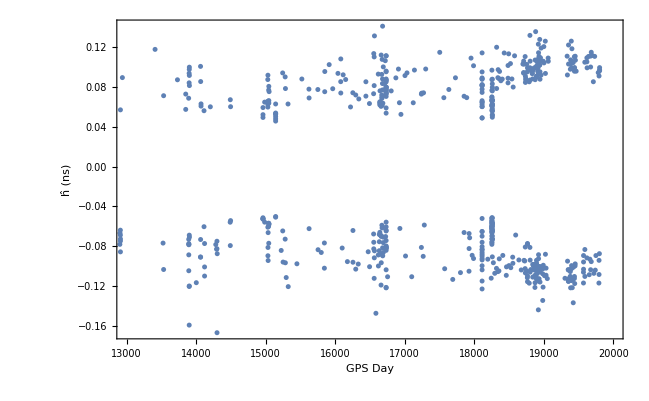

```mathematica
gpsDayHHat=ListPlot[Transpose[{gpsDays, hhat}],PlotRange->{{13000,20000},All},Frame->True,FrameTicks->Automatic,FrameTicksStyle->Directive[FontFamily->"cmr10",FontSize->20,FontColor->Black],FrameLabel->{Style["GPS Day",FontFamily->"cmr10",SingleLetterItalics->False,FontSize->25,FontColor->Black],Style["ĥ (ns)",SingleLetterItalics->False,FontFamily->"cmr10",FontSize->25,FontColor->Black]}]
```

```mathematica
(*SetDirectory[NotebookDirectory[]];*)
(*Export["gpsDayEpoch.pdf",gpsDayEpoch,"PDF",ImageSize->Full,"AllowRasterization"->False]*)
```

#### Find days with the most events, (events vs. time)

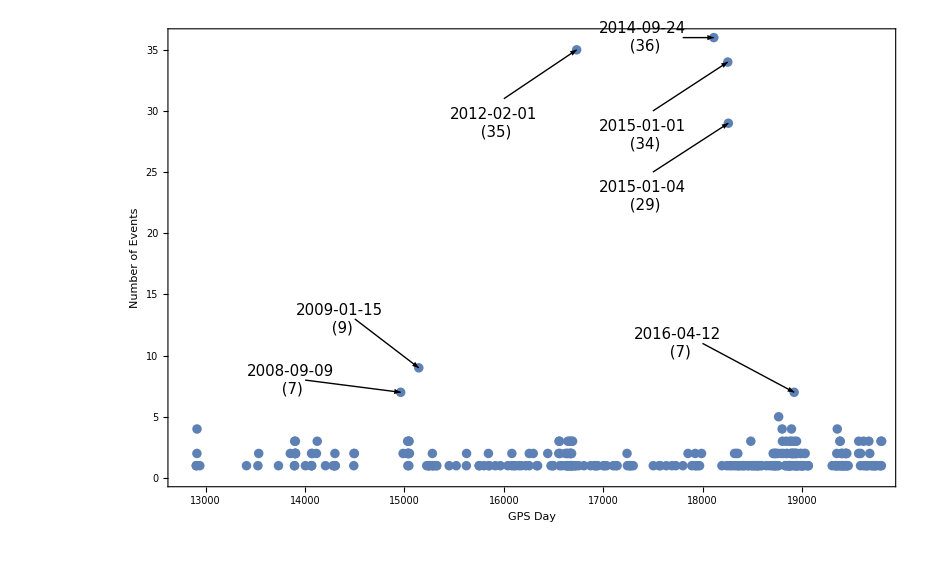

```mathematica
list=ReverseSort[Counts[gpsDays]]; (*NOTE: Use the list "list" to display a list of GPS days and events!*)
maxOccuranceDaysSorted=Keys[list]; (*This contains the GPS Days sorted from most events to least events*)
sortedMaxOccGPSDays=Sort[maxOccuranceDaysSorted];
maxOccurancesSorted=Values[list]; (*This contains the number of events for each GPS day sorted from most to least events*)
maxOccuranceCoordList=Transpose[{maxOccuranceDaysSorted,maxOccurancesSorted}];
sortedMaxOccCoordList=SortBy[maxOccuranceCoordList,First];

numEventsGPSDay1=ListPlot[sortedMaxOccCoordList,PlotRange->All,Frame->True,FrameTicks->Automatic,FrameTicksStyle->Directive[FontFamily->"cmr10",FontSize->20,FontColor->Black],FrameLabel->{Style["GPS Day",FontFamily->"cmr10",SingleLetterItalics->False,FontSize->25,FontColor->Black],Style["Number of Events",SingleLetterItalics->False,FontFamily->"cmr10",FontSize->25,FontColor->Black]}];

arrows=Graphics[{
{Arrowheads[Medium],Arrow[{{17800,36},{18113,36}}],Text[Style["2014-09-24\n (36)",FontSize->15],{17400,36}]},
{Arrowheads[Medium],Arrow[{{16000,31},{16733,35}}],Text[Style["2012-02-01\n (35)",FontSize->15],{15900,29}]},
{Arrowheads[Medium],Arrow[{{17500,30},{18254,34}}],Text[Style["2015-01-01\n (34)",FontSize->15],{17400,28}]},
{Arrowheads[Medium],Arrow[{{17500,25},{18260,29}}],Text[Style["2015-01-04\n (29)",FontSize->15],{17400,23}]},
{Arrowheads[Medium],Arrow[{{14500,13},{15144,9}}],Text[Style["2009-01-15\n (9)",FontSize->15],{14350,13}]},
{Arrowheads[Medium],Arrow[{{18000,11},{18922,7}}],Text[Style["2016-04-12\n (7)",FontSize->15],{17750,11}]},
{Arrowheads[Medium],Arrow[{{14000,8},{14962,7}}],Text[Style["2008-09-09\n (7)",FontSize->15],{13850,8}]}
}];
numEventsGPSDay=Show[numEventsGPSDay1,arrows]
```

#### Remove days with more than 1 event, plot SNRs vs. GPS Day (single-event days vs. SNRs)

```mathematica
(*The following chunk of code removes days based on number of events*)
limit=1;
singleEventDays=Table[If[sortedMaxOccCoordList[[i,2]]==limit,##&[],sortedMaxOccCoordList[[i,1]]],{i,Length[sortedMaxOccCoordList]}];
singleEventSNRs=Table[SNRs[[Position[gpsDays,singleEventDays[[i]]][[1,1]]]],{i,Length[singleEventDays]}];
singleEventAbsSNRs=Table[absSNR[[Position[gpsDays,singleEventDays[[i]]][[1,1]]]],{i,Length[singleEventDays]}];

Length[singleEventDays]

singleEventPlot=ListPlot[Transpose[{singleEventDays,singleEventSNRs}],PlotRange->{{13000,20000},{Min[SNRs],Max[SNRs]}},Frame->True,FrameTicks->{Automatic,{-20,-10,0,10,20},None},FrameTicksStyle->Directive[FontFamily->"cmr10",FontSize->20,FontColor->Black],FrameLabel->{Style["GPS Day",FontFamily->"cmr10",SingleLetterItalics->False,FontSize->25,FontColor->Black],Style["SNR",FontFamily->"cmr10",FontSize->25,FontColor->Black]} ]

singleEventAbsPlot=ListPlot[Transpose[{singleEventDays,singleEventAbsSNRs}],PlotRange->{{13000,22000},{0,Max[absSNR]}},Frame->True,FrameTicks->{Automatic,{-20,-10,0,10,20},None},FrameTicksStyle->Directive[FontFamily->"cmr10",FontSize->20,FontColor->Black],FrameLabel->{Style["GPS Day",FontFamily->"cmr10",SingleLetterItalics->False,FontSize->25,FontColor->Black],Style["|SNR|",FontFamily->"cmr10",FontSize->25,FontColor->Black]} ,Epilog->{Line[{{0,thresh},{22000,thresh}}],Text[Style["z^*=7.034",FontFamily->"cmr10",SingleLetterItalics->False,FontSize->25,FontColor->Black],{21000,thresh+0.5}]}]
```

117

```mathematica
(117/606)*100 //N
```

19.3069

#### Investigating GPS Day 18113 (a high-event day): SNRs vs. Epochs

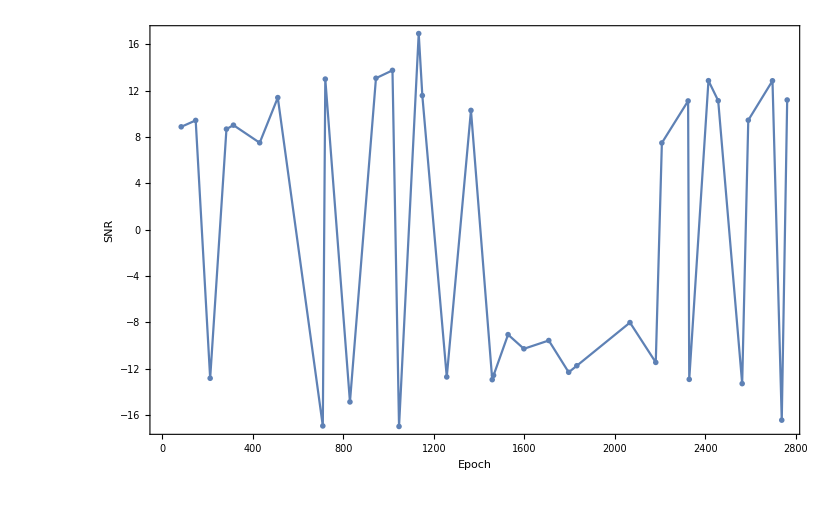

```mathematica
day18113=Flatten[Position[gpsDays,18113]];
day18113SNRs=Table[{epochs[[day18113[[i]]]],SNRs[[day18113[[i]]]]},{i,Length[day18113]}]; (*day18113SNRs contains a coodinate list (Subscript[epoch, i], Subscript[SNR, i]) for GPS Day 18113*)

ListPlot[day18113SNRs,Joined->True,PlotMarkers->Graphics@Disk[{0,0},Scaled@0.02],Frame->True,FrameTicksStyle->Directive[FontFamily->"cmr10",FontSize->20,FontColor->Black],FrameLabel->{Style["Epoch",FontFamily->"cmr10",SingleLetterItalics->False,FontSize->25,FontColor->Black],Style["SNR",FontFamily->"cmr10",FontSize->25,FontColor->Black]} ]
```

#### Investigating GPS Day 18113: Correlations between positive and negative SNRs over time

```mathematica
tempPosSNRs18113=Table[If[day18113SNRs[[i,2]]>0,day18113SNRs[[i,2]],##&[]],{i,Length[day18113SNRs]}];
negSNRs18113=Table[If[day18113SNRs[[i,2]]<0,day18113SNRs[[i,2]],##&[]],{i,Length[day18113SNRs]}];

(*Resize the length of the positive list by removing the first and last positive pairs*)
posSNRs18113=tempPosSNRs18113[[2;;Length[tempPosSNRs18113]-1]];

meanPosSNR18113=Mean[posSNRs18113];
meanNegSNR18113=Mean[negSNRs18113];

sdevPosSNR18113=StandardDeviation[posSNRs18113];
sdevNegSNR18113=StandardDeviation[negSNRs18113];

Sum[(posSNRs18113[[i]]-meanPosSNR18113)*(negSNRs18113[[i]]-meanNegSNR18113),{i,Length[posSNRs18113]}]/(Sqrt[Sum[(posSNRs18113[[i]]-meanPosSNR18113)^2,{i,Length[posSNRs18113]}]*Sum[(negSNRs18113[[i]]-meanNegSNR18113)^2,{i,Length[negSNRs18113]}]])
```

0.468754

#### Investigating GPS Day 16733: SNRs vs. Epochs

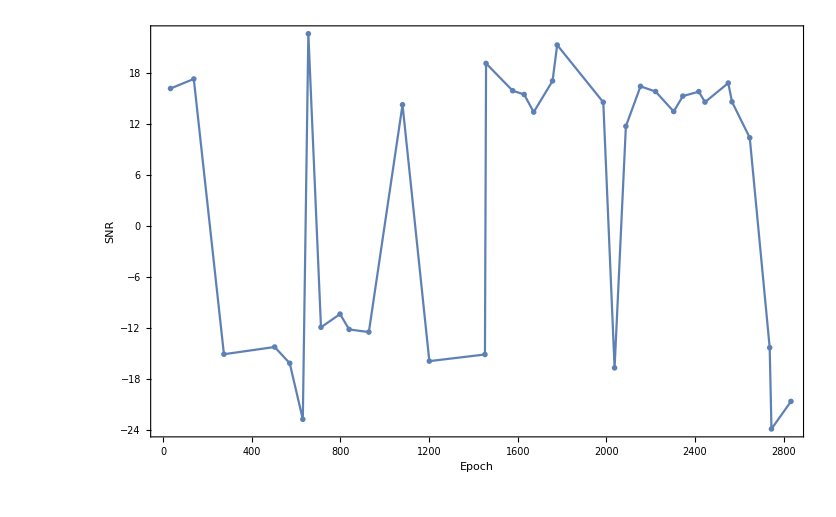

```mathematica
day16733=Flatten[Position[gpsDays,16733]];
day16733SNRs=Table[{epochs[[day16733[[i]]]],SNRs[[day16733[[i]]]]},{i,Length[day16733]}]; (*day16733SNRs contains a coodinate list (Subscript[epoch, i], Subscript[SNR, i]) for GPS Day 16733*)

ListPlot[day16733SNRs,Joined->True,PlotMarkers->Graphics@Disk[{0,0},Scaled@0.02],Frame->True,FrameTicksStyle->Directive[FontFamily->"cmr10",FontSize->20,FontColor->Black],FrameLabel->{Style["Epoch",FontFamily->"cmr10",SingleLetterItalics->False,FontSize->25,FontColor->Black],Style["SNR",FontFamily->"cmr10",FontSize->25,FontColor->Black]} ]
```

#### Graphing v_⊥ against PDF

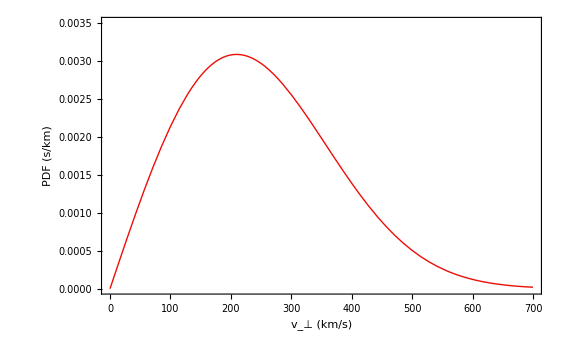

vPerpHistOnly.pdf

```mathematica
(*Event PDF of Wall-Normal Speed in Local Frame*)
vc=220;
NormVPerp=1/Integrate[vperp*(Erf[1-vperp/vc]+Erf[1+vperp/vc]),{vperp,0,∞}];
fvperp[vperp_]:=NormVPerp*vperp*(Erf[1-vperp/vc]+Erf[1+vperp/vc]);
vperpDist=Plot[fvperp[vperp],{vperp,0,700},PlotStyle->{RGBColor["#EE0E08"],Thick},PlotRange->{Automatic,{0,0.0035}},Frame->True,FrameTicksStyle->Directive[FontFamily->"cmr10",FontSize->29,FontColor->Black],FrameLabel->{Style["v_⊥ (km/s)",SingleLetterItalics->False,FontFamily->"cmr10",FontSize->30,FontColor->Black],Style["PDF (s/km)",FontFamily->"cmr10",FontSize->30,FontColor->Black]}]

vPerpHist=Histogram[vPerp,{"Raw", 23},"PDF",PlotRange->{{0,700},Automatic},ChartStyle->RGBColor["#63ACD4"],Frame->True,FrameTicksStyle->Directive[FontFamily->"cmr10",FontSize->29,FontColor->Black],FrameLabel->{Style["v_⊥ (km/s)",FontFamily->"cmr10",SingleLetterItalics->False,FontSize->30,FontColor->Black],Style["PDF",FontFamily->"cmr10",FontSize->30,FontColor->Black]}];

vPerpHistDist=Show[vPerpHist,vperpDist]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["vPerpHistOnly.pdf"]]]
```

vPerpHistDist.pdf

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["vPerpHistDist.pdf"]]]
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[cosTheta].

Histogram::ldata: cosTheta is not a valid dataset or list of datasets.

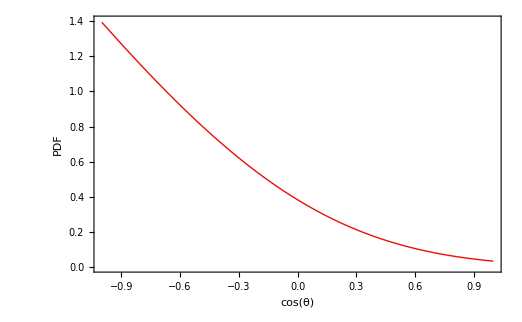

```mathematica
cosThetaHist=Histogram[cosTheta,23,"PDF",PlotRange->{{-1.02,1.02},Automatic},ChartStyle->RGBColor["#63ACD4"],Frame->True,FrameTicksStyle->Directive[FontFamily->"cmr10",FontSize->20,FontColor->Black],FrameLabel->{Style["cos(θ)",FontFamily->"cmr10",SingleLetterItalics->False,FontSize->25,FontColor->Black],Style["PDF",FontFamily->"cmr10",FontSize->25,FontColor->Black]}];

xDist1[x_]=Exp[-x^2]-Sqrt[π]*x*(1-Erf[x]);
NormConstX=1/Integrate[xDist1[x],{x,-1,1}];
xDist[x_]:=NormConstX*xDist1[x];
xDistPlot=Plot[xDist[x],{x,-1,1},PlotStyle->{RGBColor["#EE0E08"],Thick},PlotRange->{Automatic,{0,1.4}},Frame->True,FrameTicksStyle->Directive[FontFamily->"cmr10",FontSize->20,FontColor->Black],FrameLabel->{Style["cos(θ)",SingleLetterItalics->False,FontFamily->"cmr10",FontSize->25,FontColor->Black],Style["PDF",FontFamily->"cmr10",FontSize->25,FontColor->Black]}]

Show[cosThetaHist,xDistPlot]
```

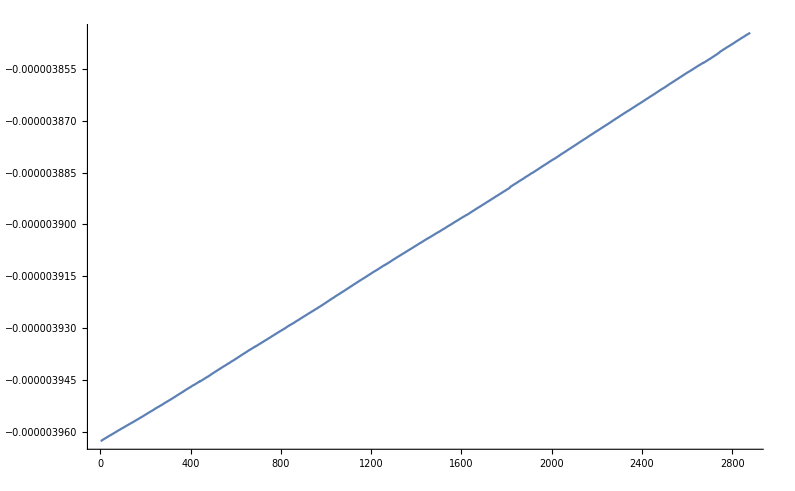

```mathematica
day18113prnG=Flatten[Import["/Users/jitensingh/Desktop/d0_data_fixed/day18113New/G06_clockTimes.txt","Table","FieldSeparators"->" "]];
ListLinePlot[day18113prnG]
```

```mathematica
lm=LinearModelFit[day18113prnG01,x,x];
ListLinePlot[Transpose[{day18113prnG01,lm["FitResiduals"]}],PlotLabel->lm["BestFit"],PlotTheme->"Detailed"]
```

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

-Graphics-